## Equilibrium calculation

```mathematica
A[α_,γ_]:=(1-γ)/(α γ);
k[α_,γ_,r_]:=(r+1)/(A[α,γ] (r-1)+r)-1;
```

```mathematica
q2=3;q1=2;β=2;α=0.8;
```

#### Type 1 anticonformists

```mathematica
α=0.8;β=0.5;
```

```mathematica
eqtype1anticonform[r_,α_,β_,γ_]:=If[γ>0.38,1/(k[α,γ,r]^(1/β)+1),1];
stable1[γ_]:=0;
stable2[γ_]:=If[γ>0.38,1];
```

```mathematica
type1anticonfdata=Import[NotebookDirectory[]<>"typeI_anticonformist_b0.5/out.csv","CSV"];
```

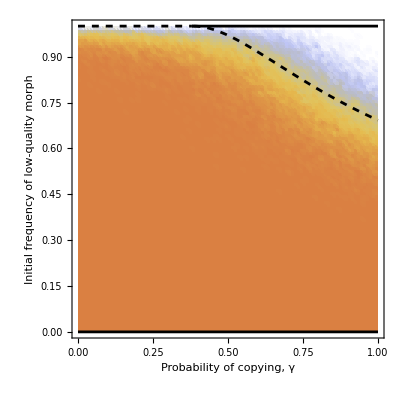

```mathematica
Show[ListDensityPlot[type1anticonfdata⟦2;;⟧,PlotRange->All,PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,5}},LegendLabel->"Equilibrium frequency of low-quality morph",LabelStyle->{FontFamily->"Calibri"}],Above],Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Probability of copying, γ",FontFamily->"Calibri",18],Style["Initial frequency of low-quality morph",FontFamily->"Calibri",18]},ColorFunction->"BeachColors"],
Plot[eqtype1anticonform[q2/q1,α,β,γ],{γ,0,1},PlotRange->{{0,1},{0,1}},PlotStyle->Directive[Dashed,Black,Thickness[0.005]],Frame->True,AspectRatio->1],
Plot[{stable1[γ],stable2[γ]},{γ,0,1},PlotRange->All,PlotStyle->Directive[Full,Black,Thickness[0.005]],Frame->True,AspectRatio->1]]
```

#### Type 2 anticonformists weak f 0.5

```mathematica
α=0.8;f=1/2;
```

```mathematica
eqtype2anticonform[r_,α_,β_,γ_]:=If[γ≥0.38,(1/(k[α,γ,r]+1)+f)/(1+f),1]
stable1[γ_]:=0;
stable2[γ_]:=If[γ>0.38,1];
```

```mathematica
type2anticonfdata=Import[NotebookDirectory[]<>"typeII_anticonformist_weak_f0.5/out.csv","CSV"];
```

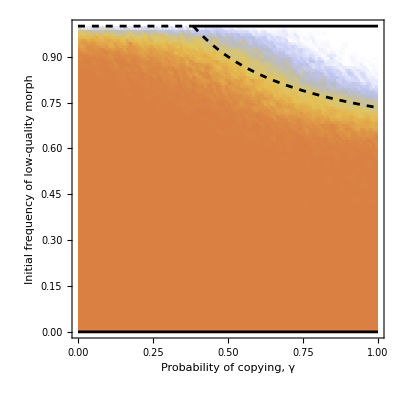

```mathematica
Show[ListDensityPlot[type2anticonfdata⟦2;;⟧,PlotRange->All,PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,5}},LegendLabel->"Equilibrium frequency of low-quality morph",LabelStyle->{FontFamily->"Calibri"}],Above],Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Probability of copying, γ",FontFamily->"Calibri",18],Style["Initial frequency of low-quality morph",FontFamily->"Calibri",18]},ColorFunction->"BeachColors"],
Plot[eqtype2anticonform[q2/q1,α,β,γ],{γ,0,1},PlotRange->{{0,1},{0,1}},PlotStyle->Directive[Dashed,Black,Thickness[0.005]],Frame->True,AspectRatio->1],
Plot[{stable1[γ],stable2[γ]},{γ,0,1},PlotRange->All,PlotStyle->Directive[Full,Black,Thickness[0.005]],Frame->True,AspectRatio->1]]
```

#### Type 2 anticonformists weak f 0.8

```mathematica
α=0.8;f=1/1.2;
```

```mathematica
eqtype2anticonform[r_,α_,β_,γ_]:=If[γ≥0.38,(1/(k[α,γ,r]+1)+f)/(1+f),1]
```

```mathematica
type2anticonfdata=Import[NotebookDirectory[]<>"typeII_anticonformist_weak_f0.8/out.csv","CSV"];
```

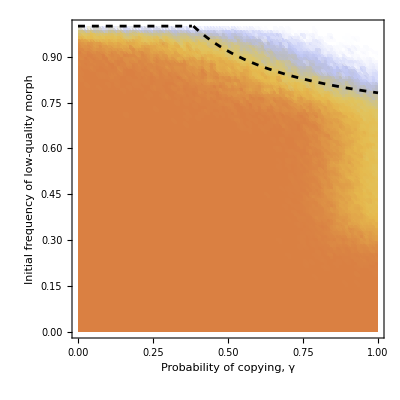

```mathematica
Show[ListDensityPlot[type2anticonfdata⟦2;;⟧,PlotRange->All,PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,5}},LegendLabel->"Equilibrium frequency of low-quality morph",LabelStyle->{FontFamily->"Calibri"}],Above],Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Probability of copying, γ",FontFamily->"Calibri",18],Style["Initial frequency of low-quality morph",FontFamily->"Calibri",18]},ColorFunction->"BeachColors"],
Plot[eqtype2anticonform[q2/q1,α,β,γ],{γ,0,1},PlotRange->{{0,1},{0,1}},PlotStyle->Directive[Dashed,Black,Thickness[0.005]],Frame->True,AspectRatio->1]]
```

#### Type 2 mixed

```mathematica
α=0.2;f=1/2;
```

```mathematica
eqtype2mixed[r_,α_,β_,γ_]:=
If[γ<0.8,1,If[γ>0.8&&γ<0.87,(1/(k[α,γ,r]+1)-f)/(1-f),0.5]];
unstable[γ_]:=1;
stable1[γ_]:=If[γ≥0.8,0.7];
stable2[γ_]:=0;
```

```mathematica
type2mixeddata=Import[NotebookDirectory[]<>"typeII_mixed_f0.5/out.csv","CSV"];
```

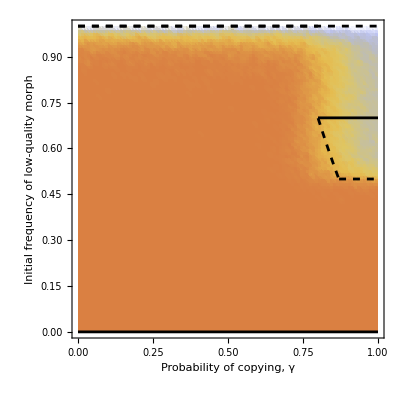

```mathematica
Show[ListDensityPlot[type2mixeddata⟦2;;⟧,PlotRange->Full,PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,5}},LegendLabel->"Equilibrium frequency of low-quality morph",LabelStyle->{FontFamily->"Calibri"}],Above],Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Probability of copying, γ",FontFamily->"Calibri",18],Style["Initial frequency of low-quality morph",FontFamily->"Calibri",18]},ColorFunction->"BeachColors"],
Plot[eqtype2mixed[q2/q1,α,β,γ],{γ,0,1},PlotRange->All,PlotStyle->Directive[Dashed,Black,Thickness[0.005]],Frame->True,AspectRatio->1],
Plot[unstable[γ],{γ,0,1},PlotRange->All,PlotStyle->Directive[Dashed,Black,Thickness[0.005]],Frame->True,AspectRatio->1],
Plot[{stable1[γ],stable2[γ]},{γ,0,1},PlotRange->All,PlotStyle->Directive[Full,Black,Thickness[0.005]],Frame->True,AspectRatio->1]]
```

#### Type 2 mixed weak - Values of Critical γ to be calculated

```mathematica
(*α=0.5;f=1/2;*)
```

```mathematica
(*eqtype2mixed[r_,α_,β_,γ_]:=If[γ<0.5,1,
If[γ>0.5&&γ<0.6,(1/(k[α,γ,r]+1)+f)/(1+f),If[γ>0.6&&γ<0.87,(1/(k[α,γ,r]+1)-f)/(1-f),0.5]]
];*)
```

```mathematica
(*type2mixeddata=Import[NotebookDirectory[]<>"typeII_mixed_weak_f0.5/out.csv","CSV"];*)
```

```mathematica
(*Show[ListDensityPlot[type2mixeddata⟦2;;⟧,PlotRange->All,PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,5}},LegendLabel->"Equilibrium frequency of low-quality morph",LabelStyle->{FontFamily->"Calibri"}],Above],Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Probability of copying, γ",FontFamily->"Calibri",18],Style["Initial frequency of low-quality morph",FontFamily->"Calibri",18]},ColorFunction->"BeachColors"],
Plot[eqtype2mixed[q2/q1,α,β,γ],{γ,0,1},PlotRange->All,PlotStyle->Directive[Black,Thickness[0.005]],Frame->True,AspectRatio->1]]*)
```